# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

## Utilities

### Feature encoders

```mathematica
standardizer=FeatureExtraction[KeyDrop["WineQuality"]@trainData,"StandardizedVector"];
```

```mathematica
StandardizeData[data_,targetName_,standardizer_]:=Block[
{
featureData=KeyDrop[targetName]@data,
targetData=KeyTake[targetName]@data,
standardizedFeatureData,
featureNames
},
standardizedFeatureData=standardizer[featureData];
featureNames=Flatten[Normal[DeleteDuplicates[Keys[featureData]]]];standardizedFeatureData=Map[<|Map[First[#]->Last[#]&,Partition[Riffle[featureNames,#],2]]|>&,standardizedFeatureData];
Dataset[Merge[#,First]&/@Partition[Riffle[standardizedFeatureData,Normal[targetData]],2]]
]
```

```mathematica
trainData=StandardizeData[trainData,"WineQuality",standardizer];
testData=StandardizeData[testData,"WineQuality",standardizer];
```

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[trainData];
```

```mathematica
GeneraliseValues[values_,scaleFactor_]:=Block[{d,min,max,newValues},
{min,max}=scaleFactor MinMax[values];
Sort[Join[values,{min,max}]]
]
```

```mathematica
(* Generalise the target feature values *)
featureValues["WineQuality"]=GeneraliseValues[featureValues["WineQuality"],1.2]
```

{3,3.6,4,5,6,7,8,9,10.8}

```mathematica
encoders=Map[RealEncoderDecoder[#,0.5]&,featureValues];
standardNetInputSize=Length[encoders]-1;
```

```mathematica
standardFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|
Splice[Map[#->ReshapeLayer[{1},"Input"->{}]&,Keys[inputEncoders]]],
"Catenate"->CatenateLayer["Output"->standardNetInputSize]
|>,
Join[
Map[#->"Catenate"&,Keys[inputEncoders]],
Map[NetPort[#]->#&,Keys[inputEncoders]]
]
]];
```

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],-1]]
]];
```

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],-1]]];
```

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

1140

### Define standard net

```mathematica
StandardNet[size_,layers_]:=Module[{standardNet,nonlin="SELU"},
standardNet=NetChain[{
LinearLayer[size,"Input"->standardNetInputSize],
ElementwiseLayer[nonlin],
Splice[Flatten[Table[{LinearLayer[size],
ElementwiseLayer[nonlin]},{i,1,layers}]]],
LinearLayer[1]
}];
NetGraph[
<|
"Features"->standardFeatureLayer,
"Net"->standardNet,
"Reshape"->ReshapeLayer[{}]
|>,
{"Features"->"Net","Net"->"Reshape",NetPort["Reshape","Output"]->NetPort["WineQuality"]}
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"]
```

### Evaluate standard net

```mathematica
NetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralNOT[size,1],
HardNeuralFlattenLayer[],
HardNeuralRealLayer[encoders["WineQuality"]["MinMax"]],
{ReshapeLayer[{}],#&}
}]
```

```mathematica
NetFlatten[NeuralLogicPredictor[64][[1]]]
```

NetGraph[<>]

```mathematica
NeuralLogicNet[size_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=NeuralLogicPredictor[size];
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet
|>,
{"FeatureLayer"->"SoftNet",NetPort["SoftNet","Output"]->NetPort["WineQuality"]}
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
Method->{"ADAM"},
TargetDevice->"GPU",
PerformanceGoal->"TrainingSpeed",
WorkingPrecision->"Mixed",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=ResourceFunction["DynamicMap"][<|
"Prediction"->First[hardNetFunction[Harden[Normal[featureLayer[#]]]]],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

### Standard baseline

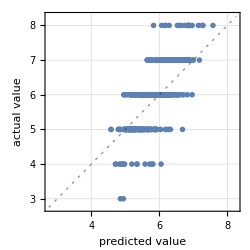
Predictor Measurements
Predictor method | RandomForest
Number of test examples | 490
Standard deviation | 0.619 ± 0.024
Standard deviation baseline | 0.876 ± 0.029
R-squared | 0.501 ± 0.051
Mean cross entropy | 0.94 ± 0.036
Single evaluation time | 6.52 ms/example
Batch evaluation speed | 2.09 examples/ms
-Graphics- |

```mathematica
p=Predict[standardizedTrainData->"WineQuality",PerformanceGoal->"Quality"];
pm=PredictorMeasurements[p,standardizedTestData]
```

### Standard NN

```mathematica
standardNet=StandardNet[64,4]
```

NetGraph[<>]

```mathematica
result=TrainStandardNet[standardNet,trainData,testData];
```

```mathematica
trainedStandardNet=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
NetMeasurements[trainedStandardNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.372981,0.627019,0.54555,0.505974,0.711318}

```mathematica
standardPredictions=NetPredict[trainedStandardNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@standardPredictions],MinMax[#["Target"]&/@standardPredictions]}
```

{{3.99866,7.28604},{3,9}}

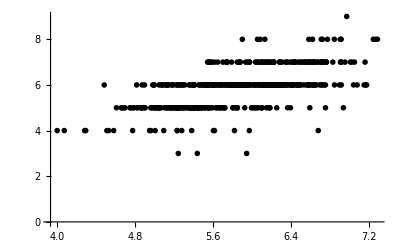

```mathematica
ListPlot[Values/@standardPredictions,PlotRange->All,PlotTheme->"Monochrome"]
```

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

536. kB

## A neural logic network

```mathematica
{softNet,hardNet}=NeuralLogicNet[128];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
result=Block[{td=Take[trainData,All],vd=testData},
TrainNeuralLogicNet[softNet,td,vd]
];
```

```mathematica
trainedNeuralLogicNet=result["TrainedNet"];
```

```mathematica
NetMeasurements[trainedNeuralLogicNet,testData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.411273,0.588727,0.47978,0.475074,0.689256}

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
```

```mathematica
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize];
```

```mathematica
predictions=NeuralLogicPredict[testData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer];
```

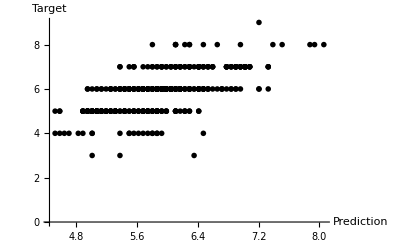

```mathematica
ListPlot[{{Missing[]},predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->"Monochrome"]
```

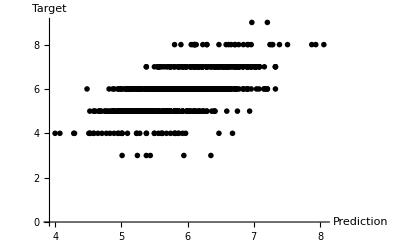

```mathematica
ListPlot[{standardPredictions,predictions},AxesLabel->Automatic,PlotRange->All,PlotTheme->"Monochrome"]
```

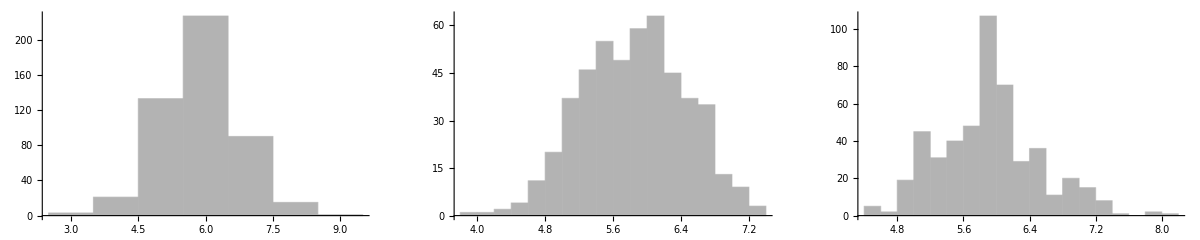

```mathematica
GraphicsRow[Histogram[#,PlotRange->All,PlotTheme->"Monochrome"]&/@{#["Target"]&/@standardPredictions,#["Prediction"]&/@standardPredictions,#["Prediction"]&/@predictions}]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

0. kB

```mathematica
standardNetSize/neuralLogicNetSize
```

standardNetSize (0.055737 /kB)

## Notes

```mathematica
neuralLogicPredictions=NetPredict[trainedNeuralLogicNet,testData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@neuralLogicPredictions],MinMax[#["Target"]&/@neuralLogicPredictions]}
```

{{4.52344,8.05781},{3,9}}

```mathematica
ListPlot[Values/@neuralLogicPredictions]
```